# Galactic Attenuation CMB

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* For decaying Dark Matter, Cirelli's tables are limited up to a DM mass of 200 TeV *)
```

```mathematica
(* from arXiv:1505.06486 *)
```

```mathematica
eVTOGeV=1. 10^-9;
kpcTOcm=3.086 10^21;
kpcTOinvGeV=kpcTOcm*cmTOinvGeV;(*GeV^-1*)
cmTOinvGeV=(1/(1.98 10^-14));(*GeV^-1*)
```

```mathematica
(* Constant definition *)
αEM=1/137;
me=0.511 10^-3;(*GeV*)
```

## optical depth on CMB

```mathematica
(* optical depth on CMB *)
```

```mathematica
(* pari production cross-section *)
σγγ[ϵc_]:=π/2 αEM^2/me^2(1-β[ϵc]^2)((3-β[ϵc]^4)Log[(1+β[ϵc])/(1-β[ϵc])]-2β[ϵc](2-β[ϵc]^2));
β[ϵc_]:=√(1-1/sCM[ϵc]);
sCM[ϵc_]:=ϵc^2/me^2;
```

```mathematica
TCMB=2.348 10^-4 *10^-9;(*GeV*)
(*
τγγCMB[enγ_,s_]:=(-4TCMB*s)/(π^2 enγ^2)NIntegrate[ϵc^3 σγγ[ϵc]Log[1-Exp[-ϵc^2/(enγ*TCMB)]],{ϵc,me,∞},MinRecursion->5]*kpcTOinvGeV;(* Assuming s (the line-of-sight) in kpc, and enγ (the photon energy) in GeV *)
*)
```

```mathematica
τγγCMBtest[enγ_,s_]:=(-4TCMB*s)/(π^2 enγ^2)NIntegrate[ϵc^3 σγγ[ϵc]Log[1-Exp[-ϵc^2/(enγ*TCMB)]],{ϵc,me,∞},Method->{Automatic,"SymbolicProcessing"->0},MaxPoints->10000]*kpcTOinvGeV;(* Assuming s (the line-of-sight) in kpc, and enγ (the photon energy) in GeV *)
```

```mathematica
τγγCMBwos[enγ_]:=(-4TCMB)/(π^2 enγ^2)NIntegrate[ϵc^3 σγγ[ϵc]Log[1-Exp[-ϵc^2/(enγ*TCMB)]],{ϵc,me,∞},MinRecursion->5]*kpcTOinvGeV;(* Assuming s (the line-of-sight) in kpc, and enγ (the photon energy) in GeV *)
```

```mathematica
(*
τγγCMBwos[enγ_]:=(-4TCMB)/(π^2 enγ^2)NIntegrate[ϵc^3 σγγ[ϵc]Log[1-Exp[-ϵc^2/(enγ*TCMB)]],{ϵc,me,∞},Method->{Automatic,"SymbolicProcessing"->0},MaxPoints->10000]*kpcTOinvGeV;(* Assuming s (the line-of-sight) in kpc, and enγ (the photon energy) in GeV *)
*)
```

```mathematica
NlogEγ=500*6+1;
LogEγmin=2.;(* GeV *)
LogEγmax=8.;(* GeV *)
EγList=Table[10^en,{en,LogEγmin,LogEγmax,(LogEγmax-LogEγmin)/(NlogEγ-1)}];
NlogEγ
```

3001

```mathematica
opticalDepthCMB=List[];
(**)
i=1;
Do[
opticalDepthCMB=Append[opticalDepthCMB,{EγList[[i]],τγγCMBwos[EγList[[i]]]}];
i++;
,{NlogEγ}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵc near {ϵc} = {0.000608153}. NIntegrate obtained -5.97866×10^-24 and 4.72455×10^-29 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵc near {ϵc} = {0.000608056}. NIntegrate obtained -6.72711×10^-24 and 5.41653×10^-29 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵc near {ϵc} = {0.000662443}. NIntegrate obtained -7.56537×10^-24 and 3.79369×10^-29 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Export["Libraries/GalOptDepthCMB_wolos_LogGeV2-8.dat",opticalDepthCMB,"Data"];
```

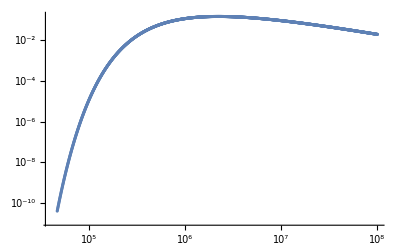

```mathematica
ListLogLogPlot[opticalDepthCMB]
```